```mathematica
w=0.0014;
z=.1;
λ=905*10^(-9);
```

```mathematica
Sqrt[0.5*(w^2-Sqrt[w^4-4*(z*λ/Pi)^2])]
```

0.0000205787

```mathematica
TextCell["Doppler Temperature","Section"]
```

Doppler Temperature

```mathematica
ω0=299792458/(905.3195*10^(-9));
Δω=60*10^(6);
M=139*1.66*10^(-27);
k=1.38*10^(-23);
c=299792458;
T = (M*c^2/(8*k*Log[2]))*(Δω/ω0)^2
```

8.89682

```mathematica
TextCell["Cell Pumpout time","Section"]
```

Cell Pumpout time

```mathematica
T=10;
len=0.01;
A=Pi*0.007^2;
mhe=4*1.66*10^(-27);
Vhe=Sqrt[8k T/(Pi*mhe)];
Vcell=(0.0125^2*Pi*len)+0.005^2*Pi*0.02;
tpump =4*Vcell/(A*Vhe)
```

0.000731867

```mathematica
TextCell["BaH-He Thermalization time","Section"]
```

BaH-He Thermalization time

```mathematica
flin=30*4.5*10^(17);
nhe=flin*4/(Vhe*A)
mfp2=1/(nhe*10^(-18)*Sqrt[139/4]);(*mean free path = 1/(cross section * density)*)
κ=(143^2)/(2*139*4);
ttherm= Sum[mfp2/Sqrt[3*k*(1/M)*(1000*E^(-n/κ)+T)],{n,0,200}]
```

9.38919×10^21

0.0000587346

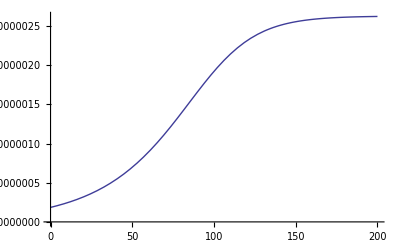

```mathematica
Plot[mfp2/Sqrt[3*k*(1/M)*(2000*E^(-n/κ)+10)],{n,0,200}]
```

```mathematica
T*(0.00012/0.00374)
```

0.320856

```mathematica
Sqrt[k*6/(4*1.66*10^(-27))]
```

111.669

```mathematica
1.2*Sqrt[k*6/(174*1.66*10^(-27))]+50*0.6*112*4/138
```

117.709

```mathematica
((1-(100/(1.4*112))^2)/4)^(-5/4)
```

10.8645

```mathematica
1.4(112)*Sqrt[1-4(11)^(-4/5)]
```

100.717

```mathematica
2ArcTan[40./120]*(180/Pi)
```

36.8699

```mathematica
dqdt = 4000;
κ=0.142;
T0 =10000;
dT= T0-300;
A = 4Pi;
1/(κ*dT*A/dqdt)
```

0.231095

```mathematica
σ=3*((663.20439)*10^(-9))^2/(2*Pi);
σD=σ*Sqrt[Pi Log[2]]*(1/250);
z=0.01;
dI=0.01;
n=dI/(σ*z);
A=.005*.005;
totn=n*A*z;
sum=0.00001*1.29615;
forvelocity=100;
IntegratedTotn=sum*A*forvelocity/(σD*z)
```

2.61404×10^9

```mathematica
(2*Pi*(1.8*2.54/2)^2)/(4*Pi*(1.5*2.54)^2)
```

0.18

```mathematica
4*Pi*(1.5*2.54)^2
```

182.415